```mathematica
SetDirectory[$UserDocumentsDirectory]
```

C:\Users\User\Documents

```mathematica
SetDirectory["C:\\Users\\User\\Documents\\mtca\\mtca_TheBook\\Chapter_7_mtca\\Images_waveletts"]
```

C:\Users\User\Documents\mtca\mtca_TheBook\Chapter_7_mtca\Images_waveletts

```mathematica
data=ReadList["rock4z"];
```

```mathematica
datalist=Flatten[data];
```

See the new OGR ms 21Oct2015, and use the equation there to calculate the Hurst exponent.
First, take the mean of the set of values, and also determine the length of the list, possibly equivalent to distance.

```mathematica
meandata=N[Mean[datalist]];
```

```mathematica
stddevndata=N[StandardDeviation[datalist]];
```

```mathematica
lengthdata=Length[datalist]
```

1262

```mathematica
%>>corrgn1R;
```

Second, determine the cumulative departures from the mean:

```mathematica
departmean=datalist-meandata;
```

```mathematica
accumdepartmean=Accumulate[departmean];
```

```mathematica
ListPlot[datalist,PlotRange->All];
```

```mathematica
ListPlot[accumdepartmean];
```

```mathematica
rangeaccumdepartmean=Max[accumdepartmean]-Min[accumdepartmean];
```

```mathematica
Flatten[Solve[rangeaccumdepartmean/stddevndata==(lengthdata/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.970662}

```mathematica
x/. %
```

0.970662

```mathematica
%>>>corrgn1R;
```

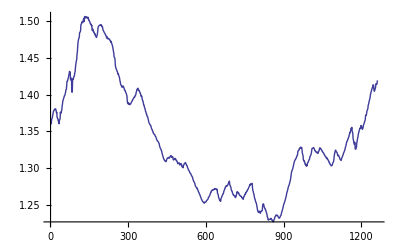

```mathematica
ListPlot[datalist,PlotRange->All,Joined->True]
```

```mathematica
ListPlot[datalist];
```

```mathematica
ListPlot[Accumulate[datalist]];
```

```mathematica
Accumulate[datalist][[-1]]
```

1689.82

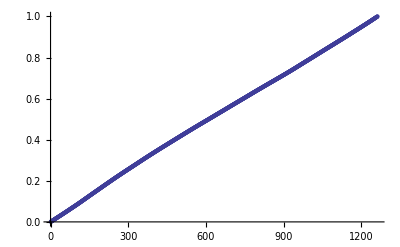

```mathematica
ListPlot[Accumulate[datalist/%],GridLines->None]
```

```mathematica
cwd=ContinuousWaveletTransform[datalist,WaveletScale->1]
```

ContinuousWaveletData[«CWT»,<9,4>,{1262}]

```mathematica
cwd[All,"Values"];
```

```mathematica
cwd[{"WaveletScale","Octaves","Voices"}]
```

{1,9,4}

ListLinePlot[cwd[All,”Values”],PlotRange→All]
ListLinePlot[cwd[All,”Values”],PlotRange→{{0,957},{-30000,30000}}]
ListLinePlot[cwd[{1,1},”Values”],PlotRange→{{0,240},{-12000,20000}}]
& so on
See Ser972_Synthesis for full details   5/12/2015
Also for details regarding EstimatedDistribution, NormalDistribution, Histogram, PDF

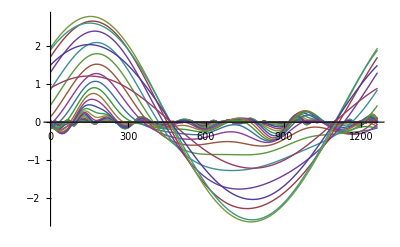

```mathematica
ListLinePlot[cwd[All,"Values"],PlotRange->All]
```

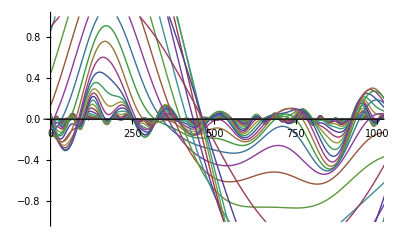

```mathematica
ListLinePlot[cwd[All,"Values"],PlotRange->{{0,1000},{-1,1}}]
```

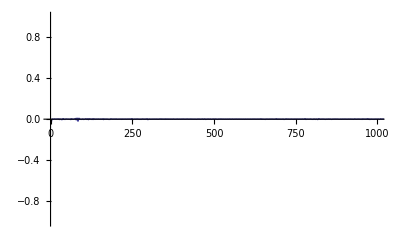

```mathematica
ListLinePlot[cwd[{1,1},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts11=Flatten[cwd[{1,1},"Values"]];
```

```mathematica
coeffts11>>corrgn1R_cwd_1_1;
```

```mathematica
meandatacoeffts11=Mean[coeffts11];
```

```mathematica
stddevndatacoeffts11=StandardDeviation[coeffts11];
```

```mathematica
lengthdatacoeffts11=Length[coeffts11];
```

```mathematica
departmeancoeffts11=coeffts11-meandatacoeffts11;
```

```mathematica
accumdepartmeancoeffts11=Accumulate[departmeancoeffts11];
```

```mathematica
rangeaccumdepartmeancoeffts11=Max[accumdepartmeancoeffts11]-Min[accumdepartmeancoeffts11];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts11/stddevndatacoeffts11==(lengthdatacoeffts11/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.567964}

```mathematica
x/. %
```

0.567964

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts12=Flatten[cwd[{1,2},"Values"]];
```

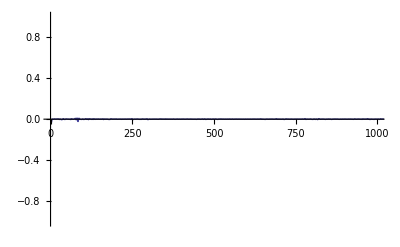

```mathematica
ListLinePlot[cwd[{1,2},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts12>>corrgn1R_cwd_1_2;
```

```mathematica
meandatacoeffts12=Mean[coeffts12];
```

```mathematica
stddevndatacoeffts12=StandardDeviation[coeffts12];
```

```mathematica
lengthdatacoeffts12=Length[coeffts12];
```

```mathematica
departmeancoeffts12=coeffts12-meandatacoeffts12;
```

```mathematica
accumdepartmeancoeffts12=Accumulate[departmeancoeffts12];
```

```mathematica
rangeaccumdepartmeancoeffts12=Max[accumdepartmeancoeffts12]-Min[accumdepartmeancoeffts12];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts12/stddevndatacoeffts12==(lengthdatacoeffts12/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.576095}

```mathematica
x/. %
```

0.576095

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts13=Flatten[cwd[{1,3},"Values"]];
```

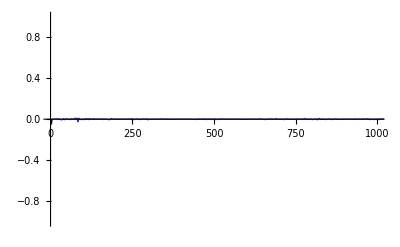

```mathematica
ListLinePlot[cwd[{1,3},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts13>>corrgn1R_cwd_1_3;
```

```mathematica
meandatacoeffts13=Mean[coeffts13];
```

```mathematica
stddevndatacoeffts13=StandardDeviation[coeffts13];
```

```mathematica
lengthdatacoeffts13=Length[coeffts13];
```

```mathematica
departmeancoeffts13=coeffts13-meandatacoeffts13;
```

```mathematica
accumdepartmeancoeffts13=Accumulate[departmeancoeffts13];
```

```mathematica
rangeaccumdepartmeancoeffts13=Max[accumdepartmeancoeffts13]-Min[accumdepartmeancoeffts13];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts13/stddevndatacoeffts13==(lengthdatacoeffts13/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.588381}

```mathematica
x/. %
```

0.588381

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts14=Flatten[cwd[{1,4},"Values"]];
```

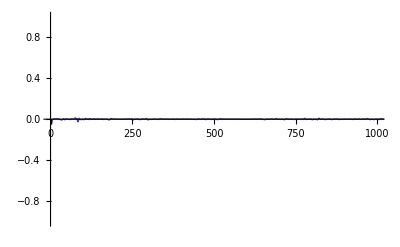

```mathematica
ListLinePlot[cwd[{1,4},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts12>>corrgn1R_cwd_1_4;
```

```mathematica
meandatacoeffts14=Mean[coeffts14];
```

```mathematica
stddevndatacoeffts14=StandardDeviation[coeffts14];
```

```mathematica
lengthdatacoeffts14=Length[coeffts14];
```

```mathematica
departmeancoeffts14=coeffts14-meandatacoeffts14;
```

```mathematica
accumdepartmeancoeffts14=Accumulate[departmeancoeffts14];
```

```mathematica
rangeaccumdepartmeancoeffts14=Max[accumdepartmeancoeffts14]-Min[accumdepartmeancoeffts14];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts14/stddevndatacoeffts14==(lengthdatacoeffts14/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.602136}

```mathematica
x/. %
```

0.602136

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts21=Flatten[cwd[{2,1},"Values"]];
```

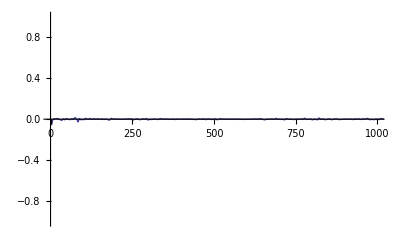

```mathematica
ListLinePlot[cwd[{2,1},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts21>>corrgn1R_cwd_2_1;
```

```mathematica
meandatacoeffts21=Mean[coeffts21];
```

```mathematica
stddevndatacoeffts21=StandardDeviation[coeffts21];
```

```mathematica
lengthdatacoeffts21=Length[coeffts21];
```

```mathematica
departmeancoeffts21=coeffts21-meandatacoeffts21;
```

```mathematica
accumdepartmeancoeffts21=Accumulate[departmeancoeffts21];
```

```mathematica
rangeaccumdepartmeancoeffts21=Max[accumdepartmeancoeffts21]-Min[accumdepartmeancoeffts21];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts21/stddevndatacoeffts21==(lengthdatacoeffts21/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.613177}

```mathematica
x/. %
```

0.613177

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts22=Flatten[cwd[{2,2},"Values"]];
```

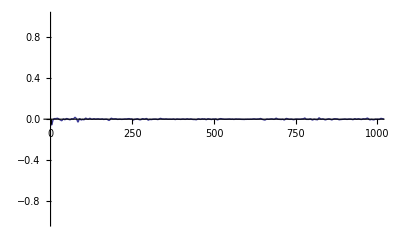

```mathematica
ListLinePlot[cwd[{2,2},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts22>>corrgn1R_cwd_2_2;
```

```mathematica
meandatacoeffts22=Mean[coeffts22];
```

```mathematica
stddevndatacoeffts22=StandardDeviation[coeffts22];
```

```mathematica
lengthdatacoeffts22=Length[coeffts22];
```

```mathematica
departmeancoeffts22=coeffts22-meandatacoeffts22;
```

```mathematica
accumdepartmeancoeffts22=Accumulate[departmeancoeffts22];
```

```mathematica
rangeaccumdepartmeancoeffts22=Max[accumdepartmeancoeffts22]-Min[accumdepartmeancoeffts22];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts22/stddevndatacoeffts22==(lengthdatacoeffts22/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.622255}

```mathematica
x/. %
```

0.622255

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts23=Flatten[cwd[{2,3},"Values"]];
```

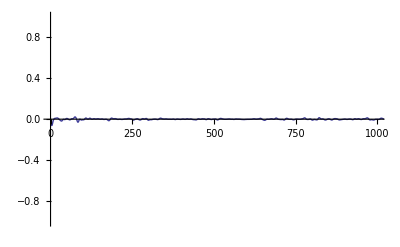

```mathematica
ListLinePlot[cwd[{2,3},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts23>>corrgn1R_cwd_2_3;
```

```mathematica
meandatacoeffts23=Mean[coeffts23];
```

```mathematica
stddevndatacoeffts23=StandardDeviation[coeffts23];
```

```mathematica
lengthdatacoeffts23=Length[coeffts23];
```

```mathematica
departmeancoeffts23=coeffts23-meandatacoeffts23;
```

```mathematica
accumdepartmeancoeffts23=Accumulate[departmeancoeffts23];
```

```mathematica
rangeaccumdepartmeancoeffts23=Max[accumdepartmeancoeffts23]-Min[accumdepartmeancoeffts23];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts23/stddevndatacoeffts23==(lengthdatacoeffts23/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.630662}

```mathematica
x/. %
```

0.630662

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts24=Flatten[cwd[{2,4},"Values"]];
```

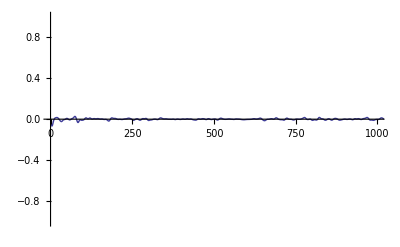

```mathematica
ListLinePlot[cwd[{2,4},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts24>>corrgn1R_cwd_2_4;
```

```mathematica
meandatacoeffts24=Mean[coeffts24];
```

```mathematica
stddevndatacoeffts24=StandardDeviation[coeffts24];
```

```mathematica
lengthdatacoeffts24=Length[coeffts24];
```

```mathematica
departmeancoeffts24=coeffts24-meandatacoeffts24;
```

```mathematica
accumdepartmeancoeffts24=Accumulate[departmeancoeffts24];
```

```mathematica
rangeaccumdepartmeancoeffts24=Max[accumdepartmeancoeffts24]-Min[accumdepartmeancoeffts24];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts24/stddevndatacoeffts24==(lengthdatacoeffts24/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.639271}

```mathematica
x/. %
```

0.639271

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts31=Flatten[cwd[{3,1},"Values"]];
```

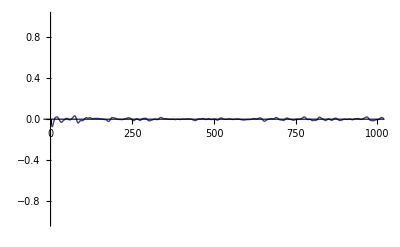

```mathematica
ListLinePlot[cwd[{3,1},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts31>>corrgn1R_cwd_3_1;
```

```mathematica
meandatacoeffts31=Mean[coeffts31];
```

```mathematica
stddevndatacoeffts31=StandardDeviation[coeffts31];
```

```mathematica
lengthdatacoeffts31=Length[coeffts31];
```

```mathematica
departmeancoeffts31=coeffts31-meandatacoeffts31;
```

```mathematica
accumdepartmeancoeffts31=Accumulate[departmeancoeffts31];
```

```mathematica
rangeaccumdepartmeancoeffts31=Max[accumdepartmeancoeffts31]-Min[accumdepartmeancoeffts31];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts31/stddevndatacoeffts31==(lengthdatacoeffts31/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.647427}

```mathematica
x/. %
```

0.647427

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts32=Flatten[cwd[{3,2},"Values"]];
```

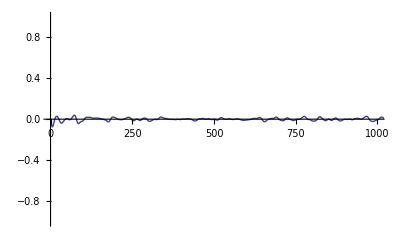

```mathematica
ListLinePlot[cwd[{3,2},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts32>>corrgn1R_cwd_3_2;
```

```mathematica
meandatacoeffts32=Mean[coeffts32];
```

```mathematica
stddevndatacoeffts32=StandardDeviation[coeffts32];
```

```mathematica
lengthdatacoeffts32=Length[coeffts32];
```

```mathematica
departmeancoeffts32=coeffts32-meandatacoeffts32;
```

```mathematica
accumdepartmeancoeffts32=Accumulate[departmeancoeffts32];
```

```mathematica
rangeaccumdepartmeancoeffts32=Max[accumdepartmeancoeffts32]-Min[accumdepartmeancoeffts32];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts32/stddevndatacoeffts32==(lengthdatacoeffts32/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.65535}

```mathematica
x/. %
```

0.65535

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts33=Flatten[cwd[{3,3},"Values"]];
```

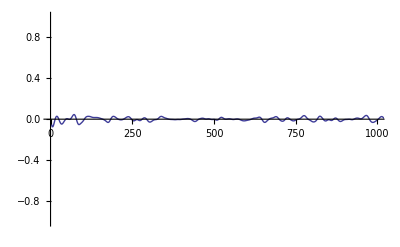

```mathematica
ListLinePlot[cwd[{3,3},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts33>>corrgn1R_cwd_3_3;
```

```mathematica
meandatacoeffts33=Mean[coeffts33];
```

```mathematica
stddevndatacoeffts33=StandardDeviation[coeffts33];
```

```mathematica
lengthdatacoeffts33=Length[coeffts33];
```

```mathematica
departmeancoeffts33=coeffts33-meandatacoeffts33;
```

```mathematica
accumdepartmeancoeffts33=Accumulate[departmeancoeffts33];
```

```mathematica
rangeaccumdepartmeancoeffts33=Max[accumdepartmeancoeffts33]-Min[accumdepartmeancoeffts33];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts33/stddevndatacoeffts33==(lengthdatacoeffts33/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.664226}

```mathematica
x/. %
```

0.664226

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts34=Flatten[cwd[{3,4},"Values"]];
```

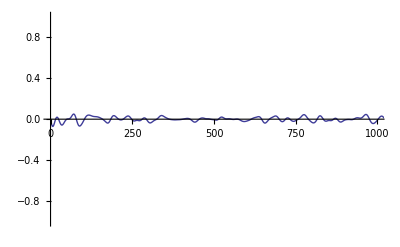

```mathematica
ListLinePlot[cwd[{3,4},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts34>>corrgn1R_cwd_3_4;
```

```mathematica
meandatacoeffts34=Mean[coeffts34];
```

```mathematica
stddevndatacoeffts34=StandardDeviation[coeffts34];
```

```mathematica
lengthdatacoeffts34=Length[coeffts34];
```

```mathematica
departmeancoeffts34=coeffts34-meandatacoeffts34;
```

```mathematica
accumdepartmeancoeffts34=Accumulate[departmeancoeffts34];
```

```mathematica
rangeaccumdepartmeancoeffts34=Max[accumdepartmeancoeffts34]-Min[accumdepartmeancoeffts34];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts34/stddevndatacoeffts34==(lengthdatacoeffts34/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.674797}

```mathematica
x/. %
```

0.674797

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts41=Flatten[cwd[{4,1},"Values"]];
```

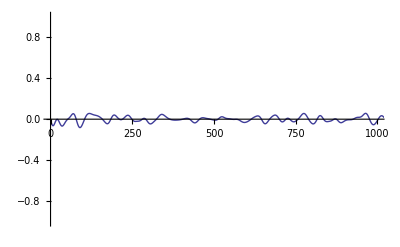

```mathematica
ListLinePlot[cwd[{4,1},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts41>>corrgn1R_cwd_4_1;
```

```mathematica
meandatacoeffts41=Mean[coeffts41];
```

```mathematica
stddevndatacoeffts41=StandardDeviation[coeffts41];
```

```mathematica
lengthdatacoeffts41=Length[coeffts41];
```

```mathematica
departmeancoeffts41=coeffts41-meandatacoeffts41;
```

```mathematica
accumdepartmeancoeffts41=Accumulate[departmeancoeffts41];
```

```mathematica
rangeaccumdepartmeancoeffts41=Max[accumdepartmeancoeffts41]-Min[accumdepartmeancoeffts41];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts41/stddevndatacoeffts41==(lengthdatacoeffts41/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.689627}

```mathematica
x/. %
```

0.689627

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts42=Flatten[cwd[{4,2},"Values"]];
```

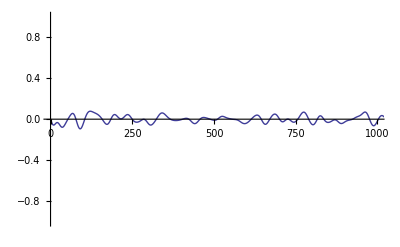

```mathematica
ListLinePlot[cwd[{4,2},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts42>>corrgn1R_cwd_4_2;
```

```mathematica
meandatacoeffts42=Mean[coeffts42];
```

```mathematica
stddevndatacoeffts42=StandardDeviation[coeffts42];
```

```mathematica
lengthdatacoeffts42=Length[coeffts42];
```

```mathematica
departmeancoeffts42=coeffts42-meandatacoeffts42;
```

```mathematica
accumdepartmeancoeffts42=Accumulate[departmeancoeffts42];
```

```mathematica
rangeaccumdepartmeancoeffts42=Max[accumdepartmeancoeffts42]-Min[accumdepartmeancoeffts42];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts42/stddevndatacoeffts42==(lengthdatacoeffts42/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.710436}

```mathematica
x/. %
```

0.710436

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts43=Flatten[cwd[{4,3},"Values"]];
```

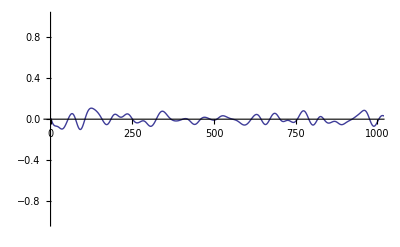

```mathematica
ListLinePlot[cwd[{4,3},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts43>>corrgn1R_cwd_4_3;
```

```mathematica
meandatacoeffts43=Mean[coeffts43];
```

```mathematica
stddevndatacoeffts43=StandardDeviation[coeffts43];
```

```mathematica
lengthdatacoeffts43=Length[coeffts43];
```

```mathematica
departmeancoeffts43=coeffts43-meandatacoeffts43;
```

```mathematica
accumdepartmeancoeffts43=Accumulate[departmeancoeffts43];
```

```mathematica
rangeaccumdepartmeancoeffts43=Max[accumdepartmeancoeffts43]-Min[accumdepartmeancoeffts43];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts43/stddevndatacoeffts43==(lengthdatacoeffts43/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.731229}

```mathematica
x/. %
```

0.731229

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts44=Flatten[cwd[{4,4},"Values"]];
```

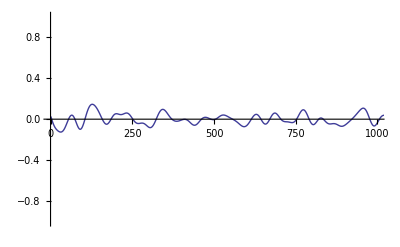

```mathematica
ListLinePlot[cwd[{4,4},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts44>>corrgn1R_cwd_4_4;
```

```mathematica
meandatacoeffts44=Mean[coeffts44];
```

```mathematica
stddevndatacoeffts44=StandardDeviation[coeffts44];
```

```mathematica
lengthdatacoeffts44=Length[coeffts44];
```

```mathematica
departmeancoeffts44=coeffts44-meandatacoeffts44;
```

```mathematica
accumdepartmeancoeffts44=Accumulate[departmeancoeffts44];
```

```mathematica
rangeaccumdepartmeancoeffts44=Max[accumdepartmeancoeffts44]-Min[accumdepartmeancoeffts44];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts44/stddevndatacoeffts44==(lengthdatacoeffts44/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.752041}

```mathematica
x/. %
```

0.752041

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts51=Flatten[cwd[{5,1},"Values"]];
```

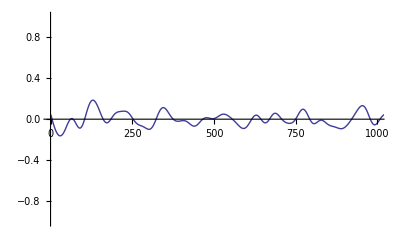

```mathematica
ListLinePlot[cwd[{5,1},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts51>>corrgn1R_cwd_5_1;
```

```mathematica
meandatacoeffts51=Mean[coeffts51];
```

```mathematica
stddevndatacoeffts51=StandardDeviation[coeffts51];
```

```mathematica
lengthdatacoeffts51=Length[coeffts51];
```

```mathematica
departmeancoeffts51=coeffts51-meandatacoeffts51;
```

```mathematica
accumdepartmeancoeffts51=Accumulate[departmeancoeffts51];
```

```mathematica
rangeaccumdepartmeancoeffts51=Max[accumdepartmeancoeffts51]-Min[accumdepartmeancoeffts51];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts51/stddevndatacoeffts51==(lengthdatacoeffts51/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.773024}

```mathematica
x/. %
```

0.773024

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts52=Flatten[cwd[{5,2},"Values"]];
```

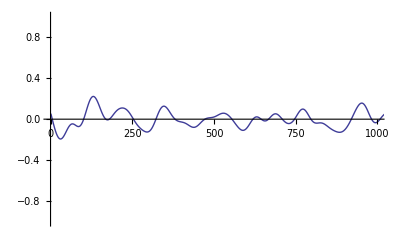

```mathematica
ListLinePlot[cwd[{5,2},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts52>>corrgn1R_cwd_5_2;
```

```mathematica
meandatacoeffts52=Mean[coeffts52];
```

```mathematica
stddevndatacoeffts52=StandardDeviation[coeffts52];
```

```mathematica
lengthdatacoeffts52=Length[coeffts52];
```

```mathematica
departmeancoeffts52=coeffts52-meandatacoeffts52;
```

```mathematica
accumdepartmeancoeffts52=Accumulate[departmeancoeffts52];
```

```mathematica
rangeaccumdepartmeancoeffts52=Max[accumdepartmeancoeffts52]-Min[accumdepartmeancoeffts52];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts52/stddevndatacoeffts52==(lengthdatacoeffts52/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.794814}

```mathematica
x/. %
```

0.794814

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts53=Flatten[cwd[{5,3},"Values"]];
```

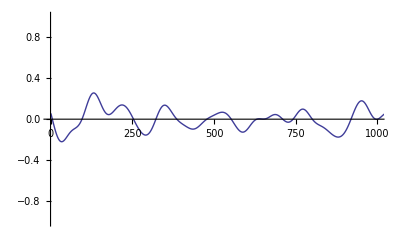

```mathematica
ListLinePlot[cwd[{5,3},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts53>>corrgn1R_cwd_5_3;
```

```mathematica
meandatacoeffts53=Mean[coeffts53];
```

```mathematica
stddevndatacoeffts53=StandardDeviation[coeffts53];
```

```mathematica
lengthdatacoeffts53=Length[coeffts53];
```

```mathematica
departmeancoeffts53=coeffts53-meandatacoeffts53;
```

```mathematica
accumdepartmeancoeffts53=Accumulate[departmeancoeffts53];
```

```mathematica
rangeaccumdepartmeancoeffts53=Max[accumdepartmeancoeffts53]-Min[accumdepartmeancoeffts53];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts53/stddevndatacoeffts53==(lengthdatacoeffts53/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.817002}

```mathematica
x/. %
```

0.817002

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts54=Flatten[cwd[{5,4},"Values"]];
```

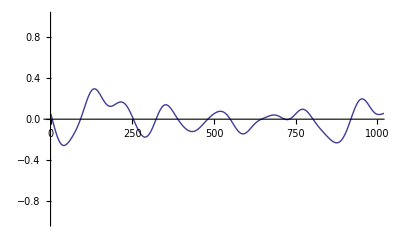

```mathematica
ListLinePlot[cwd[{5,4},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts54>>corrgn1R_cwd_5_4;
```

```mathematica
meandatacoeffts54=Mean[coeffts54];
```

```mathematica
stddevndatacoeffts54=StandardDeviation[coeffts54];
```

```mathematica
lengthdatacoeffts54=Length[coeffts54];
```

```mathematica
departmeancoeffts54=coeffts54-meandatacoeffts54;
```

```mathematica
accumdepartmeancoeffts54=Accumulate[departmeancoeffts54];
```

```mathematica
rangeaccumdepartmeancoeffts54=Max[accumdepartmeancoeffts54]-Min[accumdepartmeancoeffts54];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts54/stddevndatacoeffts54==(lengthdatacoeffts54/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.83747}

```mathematica
x/. %
```

0.83747

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts61=Flatten[cwd[{6,1},"Values"]];
```

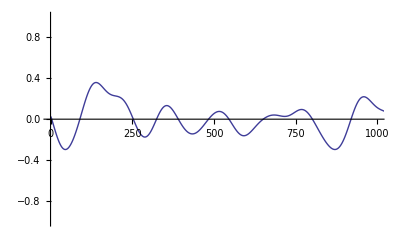

```mathematica
ListLinePlot[cwd[{6,1},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts61>>corrgn1R_cwd_6_1;
```

```mathematica
meandatacoeffts61=Mean[coeffts61];
```

```mathematica
stddevndatacoeffts61=StandardDeviation[coeffts61];
```

```mathematica
lengthdatacoeffts61=Length[coeffts61];
```

```mathematica
departmeancoeffts61=coeffts61-meandatacoeffts61;
```

```mathematica
accumdepartmeancoeffts61=Accumulate[departmeancoeffts61];
```

```mathematica
rangeaccumdepartmeancoeffts61=Max[accumdepartmeancoeffts61]-Min[accumdepartmeancoeffts61];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts61/stddevndatacoeffts61==(lengthdatacoeffts61/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.854981}

```mathematica
x/. %
```

0.854981

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts62=Flatten[cwd[{6,2},"Values"]];
```

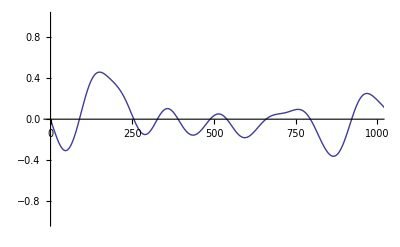

```mathematica
ListLinePlot[cwd[{6,2},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts62>>corrgn1R_cwd_6_2;
```

```mathematica
meandatacoeffts62=Mean[coeffts62];
```

```mathematica
stddevndatacoeffts62=StandardDeviation[coeffts62];
```

```mathematica
lengthdatacoeffts62=Length[coeffts62];
```

```mathematica
departmeancoeffts62=coeffts62-meandatacoeffts62;
```

```mathematica
accumdepartmeancoeffts62=Accumulate[departmeancoeffts62];
```

```mathematica
rangeaccumdepartmeancoeffts62=Max[accumdepartmeancoeffts62]-Min[accumdepartmeancoeffts62];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts62/stddevndatacoeffts62==(lengthdatacoeffts62/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.870856}

```mathematica
x/. %
```

0.870856

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts63=Flatten[cwd[{6,3},"Values"]];
```

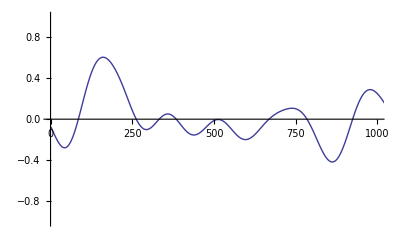

```mathematica
ListLinePlot[cwd[{6,3},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts63>>corrgn1R_cwd_6_3;
```

```mathematica
meandatacoeffts63=Mean[coeffts63];
```

```mathematica
stddevndatacoeffts63=StandardDeviation[coeffts63];
```

```mathematica
lengthdatacoeffts63=Length[coeffts63];
```

```mathematica
departmeancoeffts63=coeffts63-meandatacoeffts63;
```

```mathematica
accumdepartmeancoeffts63=Accumulate[departmeancoeffts63];
```

```mathematica
rangeaccumdepartmeancoeffts63=Max[accumdepartmeancoeffts63]-Min[accumdepartmeancoeffts63];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts63/stddevndatacoeffts63==(lengthdatacoeffts63/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.887157}

```mathematica
x/. %
```

0.887157

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts64=Flatten[cwd[{6,4},"Values"]];
```

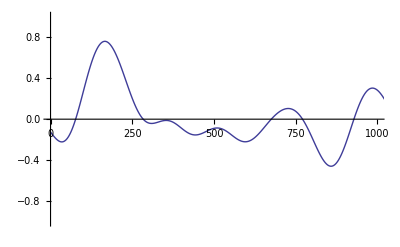

```mathematica
ListLinePlot[cwd[{6,4},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts64>>corrgn1R_cwd_6_4;
```

```mathematica
meandatacoeffts64=Mean[coeffts64];
```

```mathematica
stddevndatacoeffts64=StandardDeviation[coeffts64];
```

```mathematica
lengthdatacoeffts64=Length[coeffts64];
```

```mathematica
departmeancoeffts64=coeffts64-meandatacoeffts64;
```

```mathematica
accumdepartmeancoeffts64=Accumulate[departmeancoeffts64];
```

```mathematica
rangeaccumdepartmeancoeffts64=Max[accumdepartmeancoeffts64]-Min[accumdepartmeancoeffts64];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts64/stddevndatacoeffts64==(lengthdatacoeffts64/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.906176}

```mathematica
x/. %
```

0.906176

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts71=Flatten[cwd[{7,1},"Values"]];
```

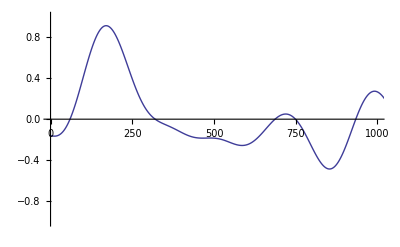

```mathematica
ListLinePlot[cwd[{7,1},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts71>>corrgn1R_cwd_7_1;
```

```mathematica
meandatacoeffts71=Mean[coeffts71];
```

```mathematica
stddevndatacoeffts71=StandardDeviation[coeffts71];
```

```mathematica
lengthdatacoeffts71=Length[coeffts71];
```

```mathematica
departmeancoeffts71=coeffts71-meandatacoeffts71;
```

```mathematica
accumdepartmeancoeffts71=Accumulate[departmeancoeffts71];
```

```mathematica
rangeaccumdepartmeancoeffts71=Max[accumdepartmeancoeffts71]-Min[accumdepartmeancoeffts71];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts71/stddevndatacoeffts71==(lengthdatacoeffts71/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.928148}

```mathematica
x/. %
```

0.928148

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts72=Flatten[cwd[{7,2},"Values"]];
```

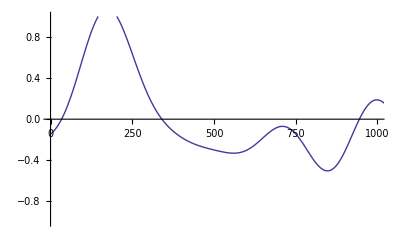

```mathematica
ListLinePlot[cwd[{7,2},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts72>>corrgn1R_cwd_7_2;
```

```mathematica
meandatacoeffts72=Mean[coeffts72];
```

```mathematica
stddevndatacoeffts72=StandardDeviation[coeffts72];
```

```mathematica
lengthdatacoeffts72=Length[coeffts72];
```

```mathematica
departmeancoeffts72=coeffts72-meandatacoeffts72;
```

```mathematica
accumdepartmeancoeffts72=Accumulate[departmeancoeffts72];
```

```mathematica
rangeaccumdepartmeancoeffts72=Max[accumdepartmeancoeffts72]-Min[accumdepartmeancoeffts72];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts72/stddevndatacoeffts72==(lengthdatacoeffts72/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.94721}

```mathematica
x/. %
```

0.94721

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts73=Flatten[cwd[{7,3},"Values"]];
```

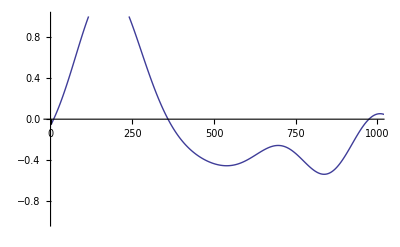

```mathematica
ListLinePlot[cwd[{7,3},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts73>>corrgn1R_cwd_7_3;
```

```mathematica
meandatacoeffts73=Mean[coeffts73];
```

```mathematica
stddevndatacoeffts73=StandardDeviation[coeffts73];
```

```mathematica
lengthdatacoeffts73=Length[coeffts73];
```

```mathematica
departmeancoeffts73=coeffts73-meandatacoeffts73;
```

```mathematica
accumdepartmeancoeffts73=Accumulate[departmeancoeffts73];
```

```mathematica
rangeaccumdepartmeancoeffts73=Max[accumdepartmeancoeffts73]-Min[accumdepartmeancoeffts73];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts73/stddevndatacoeffts73==(lengthdatacoeffts73/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.960663}

```mathematica
x/. %
```

0.960663

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts74=Flatten[cwd[{7,4},"Values"]];
```

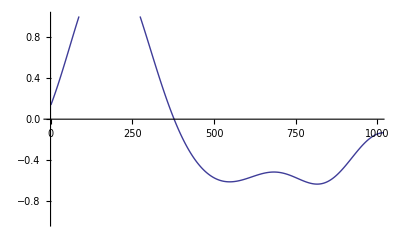

```mathematica
ListLinePlot[cwd[{7,4},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts71>>corrgn1R_cwd_7_4;
```

```mathematica
meandatacoeffts74=Mean[coeffts74];
```

```mathematica
stddevndatacoeffts74=StandardDeviation[coeffts74];
```

```mathematica
lengthdatacoeffts74=Length[coeffts74];
```

```mathematica
departmeancoeffts74=coeffts74-meandatacoeffts74;
```

```mathematica
accumdepartmeancoeffts74=Accumulate[departmeancoeffts74];
```

```mathematica
rangeaccumdepartmeancoeffts74=Max[accumdepartmeancoeffts74]-Min[accumdepartmeancoeffts74];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts74/stddevndatacoeffts74==(lengthdatacoeffts74/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.969237}

```mathematica
x/. %
```

0.969237

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts81=Flatten[cwd[{8,1},"Values"]];
```

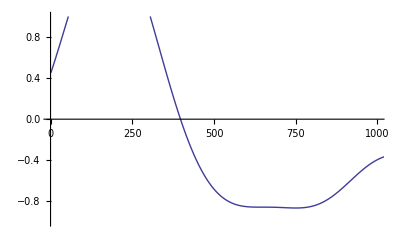

```mathematica
ListLinePlot[cwd[{8,1},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts81>>corrgn1R_cwd_8_1;
```

```mathematica
meandatacoeffts81=Mean[coeffts81];
```

```mathematica
stddevndatacoeffts81=StandardDeviation[coeffts81];
```

```mathematica
lengthdatacoeffts81=Length[coeffts81];
```

```mathematica
departmeancoeffts81=coeffts81-meandatacoeffts81;
```

```mathematica
accumdepartmeancoeffts81=Accumulate[departmeancoeffts81];
```

```mathematica
rangeaccumdepartmeancoeffts81=Max[accumdepartmeancoeffts81]-Min[accumdepartmeancoeffts81];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts81/stddevndatacoeffts81==(lengthdatacoeffts81/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.975054}

```mathematica
x/. %
```

0.975054

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts82=Flatten[cwd[{8,2},"Values"]];
```

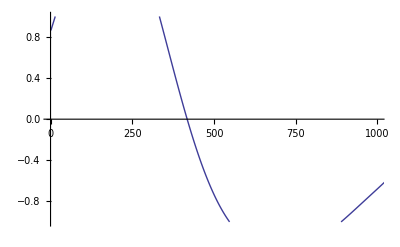

```mathematica
ListLinePlot[cwd[{8,2},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts82>>corrgn1R_cwd_8_2;
```

```mathematica
meandatacoeffts82=Mean[coeffts82];
```

```mathematica
stddevndatacoeffts82=StandardDeviation[coeffts82];
```

```mathematica
lengthdatacoeffts82=Length[coeffts82];
```

```mathematica
departmeancoeffts82=coeffts82-meandatacoeffts82;
```

```mathematica
accumdepartmeancoeffts82=Accumulate[departmeancoeffts82];
```

```mathematica
rangeaccumdepartmeancoeffts82=Max[accumdepartmeancoeffts82]-Min[accumdepartmeancoeffts82];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts82/stddevndatacoeffts82==(lengthdatacoeffts82/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.979619}

```mathematica
x/. %
```

0.979619

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts83=Flatten[cwd[{8,3},"Values"]];
```

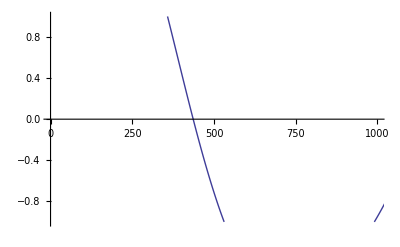

```mathematica
ListLinePlot[cwd[{8,3},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts83>>corrgn1R_cwd_8_3;
```

```mathematica
meandatacoeffts83=Mean[coeffts83];
```

```mathematica
stddevndatacoeffts83=StandardDeviation[coeffts83];
```

```mathematica
lengthdatacoeffts83=Length[coeffts83];
```

```mathematica
departmeancoeffts83=coeffts83-meandatacoeffts83;
```

```mathematica
accumdepartmeancoeffts83=Accumulate[departmeancoeffts83];
```

```mathematica
rangeaccumdepartmeancoeffts83=Max[accumdepartmeancoeffts83]-Min[accumdepartmeancoeffts83];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts83/stddevndatacoeffts83==(lengthdatacoeffts83/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.982371}

```mathematica
x/. %
```

0.982371

```mathematica
%>>>corrgn1R;
```

```mathematica
coeffts84=Flatten[cwd[{8,4},"Values"]];
```

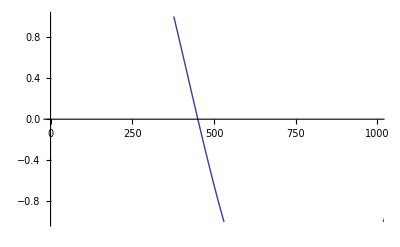

```mathematica
ListLinePlot[cwd[{8,4},"Values"],PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
coeffts84>>corrgn1R_cwd_8_4;
```

```mathematica
meandatacoeffts84=Mean[coeffts84];
```

```mathematica
stddevndatacoeffts84=StandardDeviation[coeffts84];
```

```mathematica
lengthdatacoeffts84=Length[coeffts84];
```

```mathematica
departmeancoeffts84=coeffts84-meandatacoeffts84;
```

```mathematica
accumdepartmeancoeffts84=Accumulate[departmeancoeffts84];
```

```mathematica
rangeaccumdepartmeancoeffts84=Max[accumdepartmeancoeffts84]-Min[accumdepartmeancoeffts84];
```

```mathematica
Flatten[Solve[rangeaccumdepartmeancoeffts84/stddevndatacoeffts84==(lengthdatacoeffts84/2)^x,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→0.983403}

```mathematica
x/. %
```

0.983403

```mathematica
%>>>corrgn1R;
```

```mathematica
cwd["Wavelet"]
```

MexicanHatWavelet[1]

```mathematica
{cwd["Scales"],cwd["WaveletScale"],cwd["WaveletIndex"]}
```

{{{1,1}→1.18921,{1,2}→1.41421,{1,3}→1.68179,{1,4}→2.,{2,1}→2.37841,{2,2}→2.82843,{2,3}→3.36359,{2,4}→4.,{3,1}→4.75683,{3,2}→5.65685,{3,3}→6.72717,{3,4}→8.,{4,1}→9.51366,{4,2}→11.3137,{4,3}→13.4543,{4,4}→16.,{5,1}→19.0273,{5,2}→22.6274,{5,3}→26.9087,{5,4}→32.,{6,1}→38.0546,{6,2}→45.2548,{6,3}→53.8174,{6,4}→64.,{7,1}→76.1093,{7,2}→90.5097,{7,3}→107.635,{7,4}→128.,{8,1}→152.219,{8,2}→181.019,{8,3}→215.269,{8,4}→256.,{9,1}→304.437,{9,2}→362.039,{9,3}→430.539,{9,4}→512.},1,{{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3},{4,4},{5,1},{5,2},{5,3},{5,4},{6,1},{6,2},{6,3},{6,4},{7,1},{7,2},{7,3},{7,4},{8,1},{8,2},{8,3},{8,4},{9,1},{9,2},{9,3},{9,4}}}

```mathematica
{cwd["LogScalogramFunction"],cwd["LinearScalogramFunction"]}
```

{InterpolatingFunction[{{1.,1262.},{0.25,9.}},<>],InterpolatingFunction[{{1.,1262.},{1.18921,512.}},<>]}

```mathematica
WaveletScalogram[cwd,ColorFunction->"CherryTones",Ticks->Full]
```

-Graphics-

```mathematica
cf[x_]:=Blend[{RGBColor[0.,0.,0.3],RGBColor[0.,0.,0.5],RGBColor[0,0.1,0.5],RGBColor[0,0.2,1],RGBColor[0,0.5,1],RGBColor[0.2,0.7,1],RGBColor[0.5,0.8,1],RGBColor[0.5,.9,.9],RGBColor[0.5,1.,0.9],RGBColor[0.7,1,0.7],RGBColor[0.8,1,0.5],RGBColor[1,1,0],RGBColor[1,0.8,0],RGBColor[1,0.5,0],RGBColor[1,.25,0],RGBColor[1,.1,0.],RGBColor[1,.0,0.],RGBColor[.9,.0,0.],RGBColor[0.8,0.,0.],RGBColor[0.5,0.,0.],RGBColor[.25,0.,0.],RGBColor[0.1,0,0]},x];
```

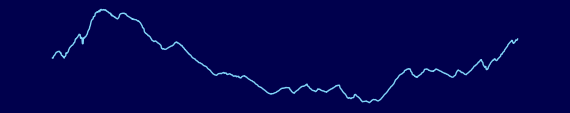
-Graphics-
-Graphics-

```mathematica
Column[{ListLinePlot[datalist,Axes->None,ImageSize->570,AspectRatio->0.2,PlotRangePadding->None,PlotRange->All,Background->cf[0],PlotStyle->cf[0.3]],WaveletScalogram[cwd,ColorFunction->(cf[#]&),Axes->True,ImageSize->570,PlotRangePadding->None,Ticks->Full]},Spacings->0.2]
```

```mathematica
ListPlot3D[cwd[All,"Values"],ColorFunction->"DarkRainbow",AxesLabel->{"depth","scale"},Mesh->None,PlotRange->All]
```

-Graphics3D-

Visualise a stationary wavelet transform using a common x axis plot . Mathematica featured example

```mathematica
dwd=StationaryWaveletTransform[datalist,Automatic,8];
```

```mathematica
Column[{ListLinePlot[datalist,ImageSize->570,AspectRatio->0.2,Axes->None,ColorFunction->"DarkRainbow",Filling->Axis,PlotLabel->Style["Data",FontFamily->"Verdana",Brown,Bold,16],InterpolationOrder->2],WaveletListPlot[dwd,DataRange->{0,1},ColorFunction->"DarkRainbow",Filling->Axis,ImageSize->570,PlotRangePadding->None,TicksStyle->Directive[13,FontFamily->"Verdana"],PlotLabel->Style["Wavelet Decomposition",FontFamily->"Verdana",Brown,Bold,16]]}]
```

-Graphics-

Visualise a stationary wavelet transform using a common y axis plot . Mathematica featured example

```mathematica
dwd=StationaryWaveletTransform[datalist,Automatic,8];
```

```mathematica
Column[{ListLinePlot[data,ImageSize->570,AspectRatio->0.2,PlotStyle->Directive[Thick,ColorData["DarkRainbow",0.2]],Axes->{False,True},TicksStyle->Directive[13,FontFamily->"Verdana"],PlotLabel->Style["Data",FontFamily->"Verdana",Brown,Bold,16],InterpolationOrder->2,ImagePadding->{{20,Automatic},{Automatic,Automatic}}],WaveletListPlot[dwd,Automatic,PlotStyle->(ColorData["DarkRainbow"]/@Riffle[#,#2]&@@Partition[Range[0.05,0.85,0.8/7],4]),ImageSize->570,PlotLayout->"CommonYAxis",Ticks->Full,TicksStyle->Directive[13,FontFamily->"Verdana"],PlotLabel->Style["Wavelet Decomposition",FontFamily->"Verdana",Brown,Bold,16],ImagePadding->{{30,Automatic},{Automatic,Automatic}}]},Alignment->Right]
```

-Graphics-